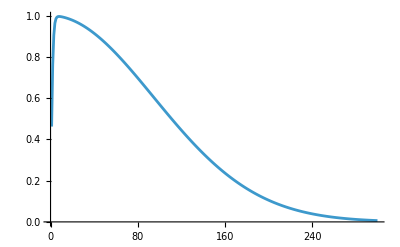

```mathematica
λ=4.5;
ListPlot[Table[Tanh[ii/2]*ⅇ^(-(ii^2)/(4*(Nx^2)/λ^2)),{ii,1,Nx}],Joined->True]
```

```mathematica
Clear[Nx,Qdis,Vn,λ];
λ=9.0;
λ=4.5;
λ=9.0;
Nx=300;
ψkx=√(2/(Nx+1.0))*Table[Sin[ii*nn*Pi/(Nx+1.0)],{nn,1,Nx},{ii,1,Nx}];
Vn[vds_]:=Block[{},
{Chop[Sum[vds[[ii]],{ii,1,Length[vds]}]],Sum[vds[[ii]]^2,{ii,1,Length[vds]}], Sum[vds[[ii]]^3,{ii,1,Length[vds]}], Sum[vds[[ii]]^4,{ii,1,Length[vds]}]}/Length[vds]
];
Qdis=Table[Tanh[ii/2]*ⅇ^(-(ii^2)/(4*(Nx^2)/λ^2)),{ii,1,Nx}];
```

```mathematica
Clear[GetVdis,Vdk,VdkQ, GetVd];
GetVdis:=Block[{vdk,ii,jj, vtpx,vtp, sum, v2},
vdk=Table[RandomReal[{-1,1}]*Qdis[[ii]],{ii,1,Nx}];
vtp=ψkx.vdk;
sum=Sum[vtp[[ii]],{ii,1,Nx}]/Nx;
vtp=Table[vtp[[ii]]-sum,{ii,1,Nx}];
v2=Sum[vtp[[ii]]^2,{ii,1,Nx}]/Nx;
vtp/√v2
];
Vdk:=Table[RandomReal[{-1,1}],{ii,1,Nx}];
VdkQ[vdk_]:=vdk*Qdis;
GetVd[vdk_]:=Block[{ii,jj, vtpx,vtp, sum, v2},
vtpx=Table[{},{ii,1,Nx}];
vtp=ψkx.vdk;
sum=Sum[vtp[[ii]],{ii,1,Nx}]/Nx;
vtp=Table[vtp[[ii]]-sum,{ii,1,Nx}];
v2=Sum[vtp[[ii]]^2,{ii,1,Nx}]/Nx;
vtp/√v2
];
```

```mathematica
Vdiss=GetVdis;
Vn[Vdiss]
```

{0,1.,0.144019,2.9116}

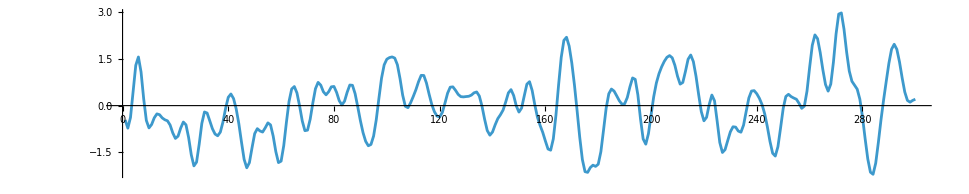

```mathematica
ListPlot[{Vdiss}, Joined->True, AspectRatio->0.2]
```

```mathematica
Vk1=Vdk;
```

```mathematica
λ=4.5;
Qdis=Table[Tanh[ii/2]*ⅇ^(-(ii^2)/(4*(Nx^2)/λ^2)),{ii,1,Nx}];
vdkq=VdkQ[Vk1];
V1=GetVd[vdkq];
Vn[V1]
```

{0,1.,-0.00951614,2.80457}

```mathematica
λ=9;
Qdis=Table[Tanh[ii/2]*ⅇ^(-(ii^2)/(4*(Nx^2)/λ^2)),{ii,1,Nx}];
vdkq=VdkQ[Vk1];
V2=GetVd[vdkq];
Vn[V2]
```

{0,1.,-0.098036,2.93041}

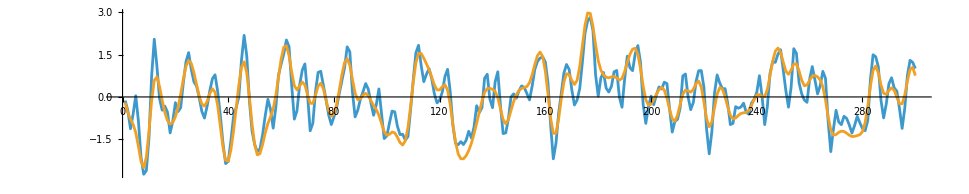

```mathematica
ListPlot[{V1,V2}, Joined->True, AspectRatio->0.2]
```